```mathematica
(*Mathematica
(*Gell-Mann SU(3)*)*)
```

```mathematica
s[1]={{0,1,0},{1,0,0},{0,0,0}};
```

```mathematica
s[2]={{0,-I,0},{I,0,0},{0,0,0}};
```

```mathematica
s[3]={{1,0,0},{0,-1,0},{0,0,0}};
```

```mathematica
s[4]={{0,0,1},{0,0,0},{1,0,0}};
```

```mathematica
s[5]={{0,0,-I},{0,0,0},{I,0,0}};
```

```mathematica
s[6]={{0,0,0},{0,0,1},{0,1,0}};
```

```mathematica
s[7]={{0,0,0},{0,0,-I},{0,I,0}};
```

```mathematica
s[8]={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3];
```

```mathematica
s[9]={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
(*Cycle:Octagon*)
```

```mathematica
Apply[Dot,Table[s[i],{i,8}]]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Table[Det[s[i]],{i,8}]
Table[Tr[s[i]],{i,8}]
```

{0,0,0,0,0,0,0,-2/(3 √3)}

{0,0,0,0,0,0,0,0}

```mathematica
(*Casimir invariant*)
ci=Sum[s[i].s[i],{i,8}]
```

{{16/3,0,0},{0,16/3,0},{0,0,16/3}}

```mathematica
(*Lehmer Salem*)
```

```mathematica
u=z/.NSolve[-1-2 z-2 z^2-2 z^3+2 z^5+2 z^6+2 z^7+z^8==0,z]
```

{-1.,-1.,-1.,0.-1. ⅈ,0.-1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,1.}

```mathematica
p[z_]=-z^8-1
```

-1-z^8

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

```mathematica
w=Table[r[i],{i,8}]
```

{-0.92388-0.382683 ⅈ,-0.92388+0.382683 ⅈ,-0.382683-0.92388 ⅈ,-0.382683+0.92388 ⅈ,0.382683-0.92388 ⅈ,0.382683+0.92388 ⅈ,0.92388-0.382683 ⅈ,0.92388+0.382683 ⅈ}

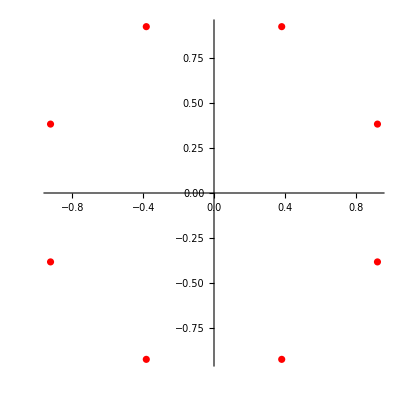

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
(*SL(3,c) matrix*)
```

```mathematica
m=(s[9]+Sum[s[i]*r[i],{i,8}])/(0.9711077442378011+8.852017913842003 ⅈ)^(1/3)
```

{{0.331818-0.559569 ⅈ,-0.108494+0.352953 ⅈ,-0.434787+0.525812 ⅈ},{-0.852105-0.261928 ⅈ,1.07543+0.0553128 ⅈ,0.+0. ⅈ},{0.525812+0.434787 ⅈ,0.743611+0.614881 ⅈ,-0.12828-0.173297 ⅈ}}

```mathematica
dt=Det[m]//Chop
```

1.

```mathematica
Tr[m]
```

1.27897-0.677553 ⅈ

```mathematica
msl=(s[9]+Sum[s[i]*(z^3-r[i]),{i,8}])/(0.9711077442378011+8.852017913842003 ⅈ)^(1/3)
```

{{(0.426322-0.225851 ⅈ) ((1.38268+0.92388 ⅈ)+z^3+((-0.92388-0.382683 ⅈ)+z^3)/(√3)),(0.426322-0.225851 ⅈ) ((0.92388+0.382683 ⅈ)+z^3-ⅈ ((0.92388-0.382683 ⅈ)+z^3)),(0.426322-0.225851 ⅈ) ((0.382683-0.92388 ⅈ)+z^3-ⅈ ((-0.382683+0.92388 ⅈ)+z^3))},{(0.426322-0.225851 ⅈ) ((0.92388+0.382683 ⅈ)+z^3+ⅈ ((0.92388-0.382683 ⅈ)+z^3)),(0.426322-0.225851 ⅈ) ((0.617317-0.92388 ⅈ)-z^3+((-0.92388-0.382683 ⅈ)+z^3)/(√3)),(0.426322-0.225851 ⅈ) ((-0.382683-0.92388 ⅈ)+z^3-ⅈ ((-0.92388+0.382683 ⅈ)+z^3))},{(0.426322-0.225851 ⅈ) ((0.382683-0.92388 ⅈ)+z^3+ⅈ ((-0.382683+0.92388 ⅈ)+z^3)),(0.426322-0.225851 ⅈ) ((-0.382683-0.92388 ⅈ)+z^3+ⅈ ((-0.92388+0.382683 ⅈ)+z^3)),(0.426322-0.225851 ⅈ) (1-(2 ((-0.92388-0.382683 ⅈ)+z^3))/(√3))}}

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/(0.05841003536719763-0.5324297767024755 ⅈ)]//Chop
```

(0.21571-1.85585 ⅈ)-(1.152+0.61029 ⅈ) z+(1.51783+2.23562 ⅈ) z^2-(1.81683+3.46908 ⅈ) z^3+(0.399776+1.12618 ⅈ) z^6+(3.072+1.62744 ⅈ) z^7+1. z^9

```mathematica
v=z/.NSolve[f[z]==0,z]
```

{-1.09783-0.148917 ⅈ,-0.517267+1.12801 ⅈ,-0.50672-0.229304 ⅈ,-0.280253+1.87177 ⅈ,-0.209823-1.17397 ⅈ,0.43737+0.670308 ⅈ,0.562796-0.554961 ⅈ,0.676621-1.68392 ⅈ,0.935111+0.120987 ⅈ}

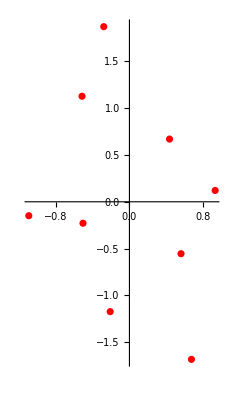

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
max=Max[Norm/@v]+0.125
```

2.01763

```mathematica
ga=ComplexPlot[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max-I*(max-0.5),max+I*(max-0.5)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100,ViewPoint->Above];
```

```mathematica
g0=JuliaSetPlot[f[x]/3.5,x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g03=ListPlot[JuliaSetPoints[f[x]/3.5,x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1,Background->White];
Export["Julia_SU3_z3_Octagon_Polynomial_scale_3p5_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g0,g03}},ImageSize->{4000,4000}]]
```

Julia_SU3_z3_Octagon_Polynomial_scale_3p5_grid.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/3.5;
		
    
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-1.45001+0.0001,1.35,1000},{-1.40001,1.4,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→"Rainbow",Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g1.jpg",g1]
```

j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g1.jpg

```mathematica
g1a=ListPlot3D[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g1a.jpg",g1a]
```

j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g1a.jpg

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g2.jpg",g2]
```

j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g2.jpg

```mathematica
g2a=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> "DarkRainbow",ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g2a.jpg",g2a]
```

j_1000_SU3_z3Octagon_Polynomial_scale_3p5_In_Out_monitor3_g2a.jpg

```mathematica
colortab=Reverse[Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g3.jpg",g3]
```

j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_g3.jpg

```mathematica
Export["j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_grid.jpg",GraphicsGrid[{{g0,g03,g2a},{ga,gb,g2}, 
 {g3,g1,g1a}},ImageSize->{6000,6000}]]
```

j_1000_SU3_z3_Octagon_Polynomial_scale_3p5_In_Out_monitor3_grid.jpg

```mathematica
(*end*)
```